```mathematica
Clear["`*"]
```

```mathematica
playlistId=2666362456;
(*playlistId=6886905093;*)
detailJson=Import["http://localhost:3000/playlist/detail?id="<>ToString@playlistId,"RawJSON"];
allJson=Import["http://localhost:3000/playlist/track/all?id="<>ToString@playlistId,"RawJSON"];
```

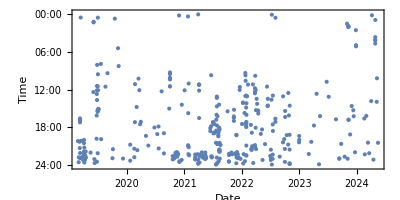

```mathematica
timezone=$TimeZone;
songs=allJson["songs"]//#["id"]->#["name"]&/@#&//Association;
groups=detailJson["playlist"]["trackIds"]//{#["id"],#["at"],songs[#["id"]]}&/@#&;
(*groups=Select[groups,1<=DateValue[FromUnixTime[#[[2]]/1000,TimeZone->timezone],"ISOWeekDay"]<=5&];*)
(*groups=Select[groups,<FromUnixTime[#[[2]]/1000,TimeZone->timezone]<=&];*)
timestamps=groups//#[[2]]/1000&/@#&;
data=(Module[{id,at,name,time},{id,at,name}={#[[1]],#[[2]],#[[3]]};
time=FromUnixTime[at/1000,TimeZone->timezone];
Tooltip[{time,DateValue[time,"HourExact"]},Row[{name,time}]]]&)/@groups;
DateListPlot[data,Joined->False,ScalingFunctions->"Reverse",AspectRatio->1/2,FrameLabel->{"Date","Time"},ImageSize->Full,FrameTicks->{{Table[{x,StringRepeat["0",2-StringLength[ToString@x]]<>ToString@x<>":00"},{x,0,24,2}],None},{Automatic,None}},PlotRange->{Automatic,{-0.2,24.2}}]
```